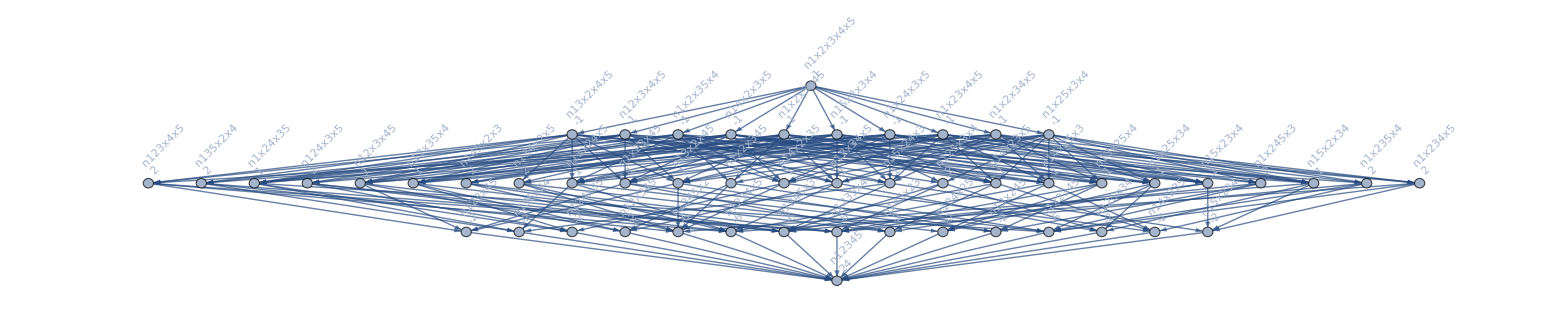
-Graphics- | 24 x-50 x^2+35 x^3-10 x^4+x^5

```mathematica
Monitor[Table[With[{g=MobiusGraph[k]},{g,ChromaticPolynomial[allGraphs[k,"graph"],x]}],{k,Select[atomKeys,VertexCount[allGraphs[#,"graph"]]==5&]}],k]//Sort//TableForm
```

```mathematica
TableForm[Monitor[Table[With[{g=MobiusGraph[k]},{VertexCount[g],EdgeCount[g]}],{k,Select[Keys[allGraphs],VertexCount[allGraphs[#,"graph"]]==3&]}],k]//Sort//Tally,TableDepth->1]
```

{{1,0},25}
{{2,1},75}
{{4,4},75}
{{5,6},25}

```mathematica
CoeffRealNull2[exp_,k_]:=Table[With[{v=Coefficient[exp,var]},v],{var,Select[sorted,StringCount[SymbolName[#],"x"]==k&]}]
```

```mathematica
Select[sorted,StringCount[SymbolName[#],"x"]==1&]
```

{n1x2345,n15x234,n14x235,n145x23,n13x245,n135x24,n134x25,n1345x2,n12x345,n125x34,n124x35,n1245x3,n123x45,n1235x4,n1234x5}

```mathematica
allGraphs[k5Key,"colofourrealnull"]
```

24 n12345-6 n1234x5-6 n1235x4-2 n123x45+2 n123x4x5-6 n1245x3-2 n124x35+2 n124x3x5-2 n125x34+2 n125x3x4-2 n12x345+n12x34x5+n12x35x4+n12x3x45-n12x3x4x5-6 n1345x2-2 n134x25+2 n134x2x5-2 n135x24+2 n135x2x4-2 n13x245+n13x24x5+n13x25x4+n13x2x45-n13x2x4x5-2 n145x23+2 n145x2x3-2 n14x235+n14x23x5+n14x25x3+n14x2x35-n14x2x3x5-2 n15x234+n15x23x4+n15x24x3+n15x2x34-n15x2x3x4-6 n1x2345+2 n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5

```mathematica
With[
{count=0,keys={alfa1Key,delta1Key,gamma1Key,beta1Key,epsilon1Key,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key,k5Key}},
MatrixForm[
Transpose[
Table[
CoeffRealNull2[allGraphs[k,"colofourrealnull"],count],{k,keys}]
],
TableHeadings->{Map[{#,#/.repRealDemo }&,Select[sorted,StringCount[SymbolName[#],"x"]==count&]],Table[allGraphs[k,"graph"],{k,keys}]}
]
]
```

( | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
{n12345,68} | 2 | 2 | 2 | 2 | 2 | -6 | -6 | -6 | -6 | -6 | 24)

```mathematica
With[
{count=1,keys={alfa1Key,delta1Key,gamma1Key,beta1Key,epsilon1Key,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key,k5Key}},
MatrixForm[
Transpose[
Table[
CoeffRealNull2[allGraphs[k,"colofourrealnull"],count],{k,keys}]
],
TableHeadings->{Map[{#,#/.repRealDemo }&,Select[sorted,StringCount[SymbolName[#],"x"]==count&]],Table[allGraphs[k,"graph"],{k,keys}]}
]
]
```

( | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
{n1x2345,131} | 0 | 0 | -1 | 0 | 0 | 0 | 2 | 2 | 0 | 2 | -6
{n15x234,170} | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -2
{n14x235,98} | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 2 | 1 | -2
{n145x23,211} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -2
{n13x245,96} | -1 | -1 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | -2
{n135x24,96} | -1 | 0 | -1 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | -2
{n134x25,106} | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 1 | 2 | -2
{n1345x2,136} | 0 | 0 | 0 | 0 | -1 | 2 | 0 | 2 | 2 | 0 | -6
{n12x345,146} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -2
{n125x34,163} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2
{n124x35,93} | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 2 | 1 | 0 | -2
{n1245x3,136} | 0 | 0 | 0 | -1 | 0 | 0 | 2 | 0 | 2 | 2 | -6
{n123x45,170} | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -2
{n1235x4,136} | 0 | -1 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | -6
{n1234x5,172} | -1 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 2 | 0 | -6)

```mathematica
With[
{count=2,keys={alfa1Key,delta1Key,gamma1Key,beta1Key,epsilon1Key,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key,k5Key}},
MatrixForm[
Transpose[
Table[
CoeffRealNull2[allGraphs[k,"colofourrealnull"],count],{k,keys}]
],
TableHeadings->{Map[{#,#/.repRealDemo }&,Select[sorted,StringCount[SymbolName[#],"x"]==count&]],Table[allGraphs[k,"graph"],{k,keys}]}
]
]
```

( | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
{n1x2x345,364} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 2
{n1x25x34,328} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1
{n1x24x35,200} | 0 | 0 | 1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1
{n1x245x3,262} | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 2
{n1x23x45,450} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
{n1x235x4,262} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 2
{n1x234x5,438} | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 2
{n15x2x34,452} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
{n15x24x3,340} | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1
{n15x23x4,496} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
{n14x2x35,232} | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | -1 | 0 | 1
{n14x25x3,256} | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 1
{n14x23x5,446} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1
{n145x2x3,524} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 2
{n13x2x45,340} | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1
{n13x25x4,274} | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 1
{n13x24x5,286} | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 1
{n135x2x4,272} | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 2
{n134x2x5,344} | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 2
{n12x3x45,406} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
{n12x35x4,292} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1
{n12x34x5,478} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
{n125x3x4,420} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2
{n124x3x5,344} | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 2
{n123x4x5,544} | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 2)

```mathematica
With[
{count=3,keys={alfa1Key,delta1Key,gamma1Key,beta1Key,epsilon1Key,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key,k5Key}},
MatrixForm[
Transpose[
Table[
CoeffRealNull2[allGraphs[k,"colofourrealnull"],count],{k,keys}]
],
TableHeadings->{Map[{#,#/.repRealDemo }&,Select[sorted,StringCount[SymbolName[#],"x"]==count&]],Table[allGraphs[k,"graph"],{k,keys}]}
]
]
```

( | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
{n1x2x3x45,1208} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
{n1x2x35x4,728} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
{n1x2x34x5,1240} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
{n1x25x3x4,876} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
{n1x24x3x5,876} | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
{n1x23x4x5,1380} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
{n15x2x3x4,1344} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
{n14x2x3x5,1112} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
{n13x2x4x5,1088} | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
{n12x3x4x5,1368} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
With[
{count=4,keys={alfa1Key,delta1Key,gamma1Key,beta1Key,epsilon1Key,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key,k5Key}},
MatrixForm[
Transpose[
Table[
CoeffRealNull2[allGraphs[k,"colofourrealnull"],count],{k,keys}]
],
TableHeadings->{Map[{#,#/.repRealDemo }&,Select[sorted,StringCount[SymbolName[#],"x"]==count&]],Table[allGraphs[k,"graph"],{k,keys}]}
]
]
```

( | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
{n1x2x3x4x5,3728} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
ChromaticPolynomial[CompleteGraph[4],x]//CompleteBaseCoeff
```

{0,0,0,0,1}